# Math 223: Homework 8

Ali Heydari

April 1st, 2021

## Problem 1

Find the asymptotic behavior of 



as x→ ∞ up to terms involving 1/x^2.

Since  is monotonic on the interval [0,2], we can find the solution through iterative; specifically, I(x) = ∫_a^b f(t) ⅇ^(ⅈ x t)ⅆt∼ ∑_(n=0)^∞ (-1)^n/(ⅈ x)^(n+1)[f^(n)(b) ⅇ^(ⅈ x b)-f^(n)(a) ⅇ^(ⅈ x a)],   x→+∞, where f(t) = sin(t) + t . Going up to two terms, we have: 

I(x) ~ 1/(ⅈ x)[sin(2) ⅇ^(2ⅈ x) + 2 ⅇ^(2ⅈ x)]+1/(ⅈ x)^2[cos(2) ⅇ^(2ⅈ x)+2 ⅇ^(2ⅈ x)-cos(0) ⅇ^(ⅈ x 0)] +∑_(n=3)^∞ (-1)^n/(ⅈ x)^(n+1)[f^(n)(2) ⅇ^(ⅈ x 2)-f^(n)(0) ⅇ^(ⅈ x 0)]  

I(x) ~ 1/(ⅈ x)sin(2) ⅇ^(2ⅈ x)-2 ⅇ^(2ⅈ x)-1/x^2[(cos(2) + 1) ⅇ^(2ⅈ x)+ 2] 
So now we save this solution for future use:

```mathematica
approxSol[x_] = -(ⅈ (2+Sin[2])ⅇ^(2 ⅈ x))/x+ⅇ^(2 ⅈ x)/x^2(1+ Cos[2])-2/x^2
```

-2/x^2+(ⅇ^(2 ⅈ x) (1+Cos[2]))/x^2-(ⅈ ⅇ^(2 ⅈ x) (2+Sin[2]))/x

Now to compare our solution with the exact solution:

```mathematica
exactSol[x_]=Integrate[Sin[t]*E^(I*x*t) + t*E^(I*x*t),{t,0,2}]
```

(-1+ⅇ^(2 ⅈ x) (1-2 ⅈ x))/x^2+(-1+ⅇ^(2 ⅈ x) (Cos[2]-ⅈ x Sin[2]))/(-1+x^2)

Resulting in:

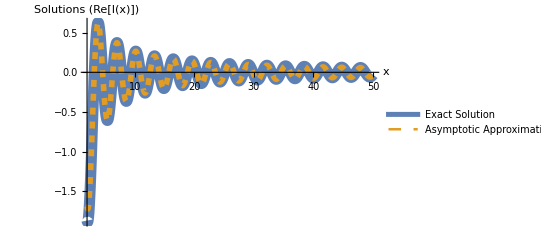

```mathematica
Plot[{Re[exactSol[x]],Re[approxSol[x]]},{x,2,50}, PlotRange->All,
PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Solutions (Re[I(x)])", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact Solution","Asymptotic Approximation"}]
```

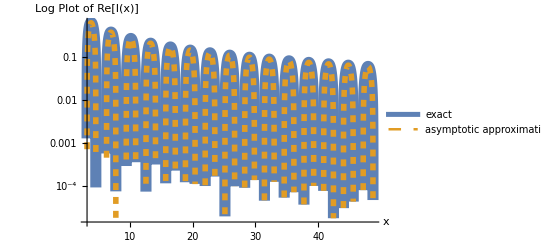

```mathematica
LogPlot[{Re[exactSol[x]],Re[approxSol[x]]},{x,2,50}, PlotRange->All,
PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Log Plot of Re[I(x)]", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact","asymptotic approximation"}]
```

these plots show great agreement as x→ ∞, as desired. This is a good verification that our approach worked well and that we have characterized the asymptotic behavior of the solution well.

## Problem 2

Use the method of stationary phase to find the leading behaviors of the following integrals as x→ ∞.

(a)

We know that the method of stationary phase will give us the leading asymptotic behavior of generalized Fourier integrals that have stationary points, i.e. given ,  at some point in the interval. We can also see that , but . Knowing this, we can see that the stationary point of  will be at , since . However, we want to do a substitution for the change of variables, so that we can actually perform the method of stationary phase. That is:

let  and . So now we rewrite the integral as:


Now we take , which means that the Taylor expansion of this function will have a leading constant plus polynomials in terms of . That is:

```mathematica
Series[Tan[Sqrt[u]]/Sqrt[u],{u,0,5}]
```

1+u/3+(2 u^2)/15+(17 u^3)/315+(62 u^4)/2835+(1382 u^5)/155925+O[u]^(11/2)

which is almost what we had before, except now we have taken care of the  term. So now we take the limits of integration to infinity, and obtain:

```mathematica
approxSol = 1/2 * Integrate[E^(I*x*u^2),{u,0,∞}, Assumptions->Im[x]>0]
```

(√π)/(4 √(-ⅈ x))

Now we want to check out solution with what he numerical solution computes:

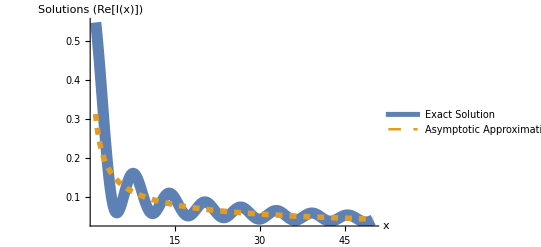

```mathematica
Plot[{Re[NIntegrate[(Tan[t])*E^(I*x*t^4),{t,0,1}]], Re[approxSol]},{x,1,50}, PlotRange->All,
PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Solutions (Re[I(x)])", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact Solution","Asymptotic Approximation"}]
```

Which is pretty terrible actually... so let’s see what Mathematica’s solution computes:

```mathematica
mathematicaAsymp = AsymptoticIntegrate[(Tan[t])*E^(I*x*t^4),{t,0,1},x-> ∞]
```

1/4 ⅇ^((ⅈ π)/4) √π √(1/x)

comparing all three now:

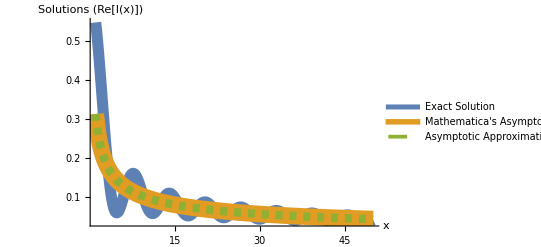

```mathematica
Plot[{Re[NIntegrate[(Tan[t])*E^(I*x*t^4),{t,0,1}]],Re[mathematicaAsymp ], Re[approxSol]},{x,1,50}, PlotRange->All,
PlotStyle-> {Directive[Solid,Thickness[0.02]],Directive[Solid,Thickness[0.03]], Directive[Dashed,Thickness[0.015]]},AxesLabel->{Style["x",Italic,18],Style["Solutions (Re[I(x)])", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact Solution","Mathematica's Asymptotic","Asymptotic Approximation" }]
```

So we do just as bad (or just as well) as Mathematica’s asymptotic solve. This is somewhat comforting at least ...

(b)

Once again we want to use the method of stationary phase for finding the leading behavior of this integral. We have that , resulting in the stationary points to be at -1 and 1 (since ), but since we are on the positive axis, we only care for 1. 

Following the process of Stationary Phase method, we can rewrite the original integral as:

using the Riemann-Lebesgue lemma, we can see that  and  will tend to 0, so all we are left with now is .  So now we must find , which would be the second derivative since . So now we expand  to get: 


Similarly, taking , we take the exact value at the stationary point, i.e. f(1) = 2. So now we have:

 

So now we can integrate this value to see what our approximation will yield:

```mathematica
approx =  2 * Integrate[E^(I*x*(-2/3 +(t-1)^2)),{t,-∞,∞}, Assumptions->Im[x]>0]
```

(2 ⅇ^(-(2 ⅈ x)/3) √π)/(√(-ⅈ x))

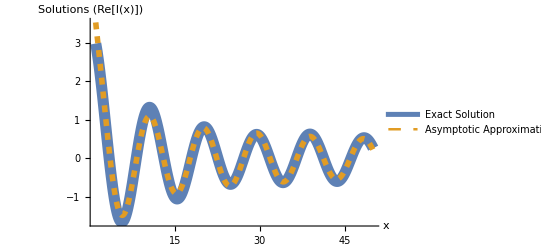

```mathematica
Plot[{Re[NIntegrate[(1+t)*E^(I*x*((t^3/3)-t)),{t,1/2,2}]], Re[approx]},{x,1,50}, PlotRange->All,
PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Solutions (Re[I(x)])", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact Solution","Asymptotic Approximation"}]
```

Which shows much better agreement between our asymptotic solution and the exact (numerical) solution. To compare our solutions with the Mathematica’s Asymptotic solution:

```mathematica
mathematicaAsymp = AsymptoticIntegrate[(1+t)*E^(I*x*((t^3/3)-t)),{t,1/2,2},x-> ∞]
```

(2 ⅇ^((ⅈ π)/4-(2 ⅈ x)/3) √π)/(√x)

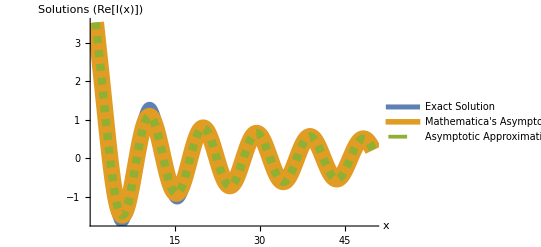

```mathematica
Plot[{Re[NIntegrate[(1+t)*E^(I*x*((t^3/3)-t)),{t,1/2,2}]],Re[mathematicaAsymp ], Re[approx]},{x,1,50}, PlotRange->All,
PlotStyle-> {Directive[Solid,Thickness[0.02]],Directive[Solid,Thickness[0.03]], Directive[Dashed,Thickness[0.015]]},AxesLabel->{Style["x",Italic,18],Style["Solutions (Re[I(x)])", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact Solution","Mathematica's Asymptotic","Asymptotic Approximation" }]
```

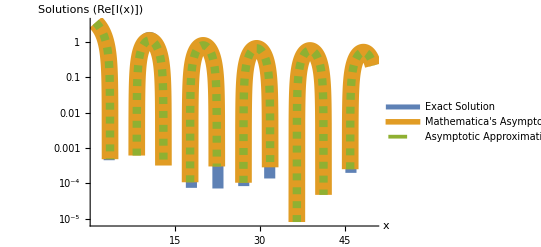

```mathematica
LogPlot[{Re[NIntegrate[(1+t)*E^(I*x*((t^3/3)-t)),{t,1/2,2}]],Re[mathematicaAsymp ], Re[approx]},{x,1,50}, PlotRange->All,
PlotStyle-> {Directive[Solid,Thickness[0.02]],Directive[Solid,Thickness[0.03]], Directive[Dashed,Thickness[0.015]]},AxesLabel->{Style["x",Italic,18],Style["Solutions (Re[I(x)])", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact Solution","Mathematica's Asymptotic","Asymptotic Approximation" }]
```

Which show both our solution and Mathematica’s solution to match very closely with the numerical solution, which is a good sign!